## Set up the models and the standard parameters

The goal here is to re-connect the ideas of the models and the parameters we had before to try and think about some implied landscape where we can see what the distribution is of the probability that some organisms will end up using the same space on a landscape.

```mathematica
(*Define constants*)
R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
γ=150;
δ=0.5;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Define grid size for the landscape*)
gridSize={50,50}; (*adjust for larger or smaller landscapes*)

(*Generate random values for T and S across the grid*)
meanT = 20;
varT = 0.5;
alphaS = 2;
betaS = 1;
Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
Sgrid=RandomVariate[GammaDistribution[alphaS,betaS],gridSize];

(*Compute probabilities w_{i,j} across the landscape*)
(*Truncate landscape probabilities to be>=0*)landscapeProbabilities=Table[Max[0,w[Tgrid[[i,j]],Sgrid[[i,j]]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];
```

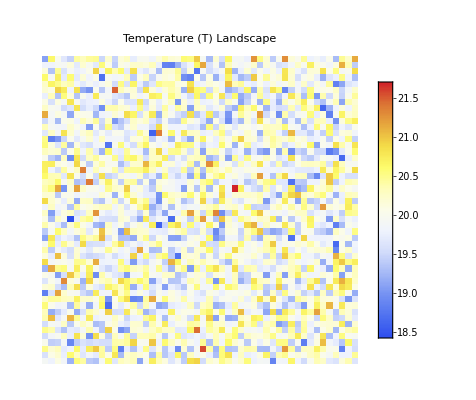
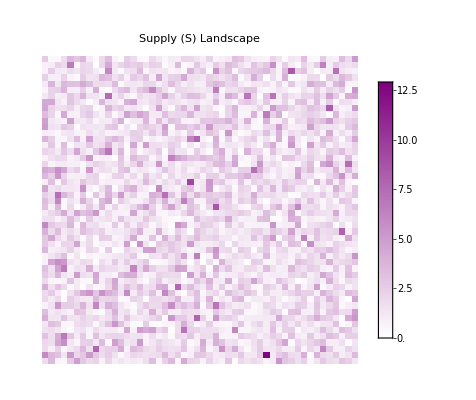
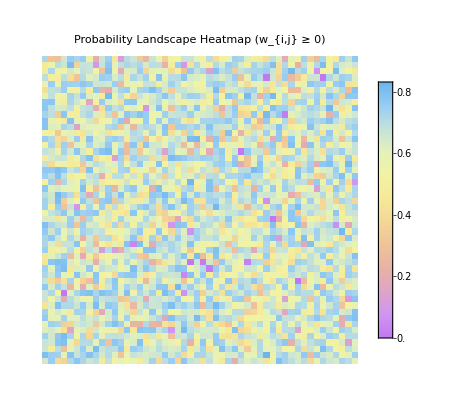
-Graphics- | -Graphics-
 | -Graphics-

```mathematica
(*Heatmap for w_{i,j} values with Magma color scheme*)heatmapW=ArrayPlot[landscapeProbabilities,ColorFunction->"Pastel",Mesh->False,PlotLabel->"Probability Landscape Heatmap (w_{i,j} ≥ 0)",PlotLegends->Automatic];

(*Heatmap for T values with TemperatureMap color scheme*)
heatmapT=ArrayPlot[Tgrid,ColorFunction->"TemperatureMap",Mesh->False,PlotLabel->"Temperature (T) Landscape",PlotLegends->Automatic];

(*Heatmap for S values with purple gradient color scheme*)
heatmapS=ArrayPlot[Sgrid,ColorFunction->(Blend[{White,Purple},#]&),Mesh->False,PlotLabel->"Supply (S) Landscape",PlotLegends->Automatic];


(*Arrange the plots in a grid with T and S on the top row,w at double size on the second row*)Grid[{{heatmapT,heatmapS},{SpanFromLeft,heatmapW}},Spacings->{2,1}]
```

DensityPlot::argrx: DensityPlot called with 2 arguments; 3 arguments are expected.

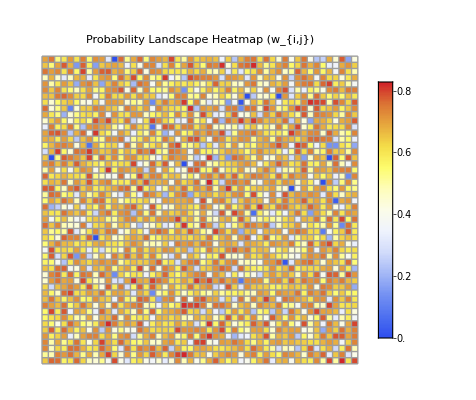
-Graphics-
DensityPlot[0.00605788 ⅇ^(-720.562 (-0.827542+x)^2)+0.0121158 ⅇ^(-720.562 (-0.824246+x)^2)+0.0181736 ⅇ^(-720.562 (-0.820949+x)^2)+0.0181736 ⅇ^(-720.562 (-0.817653+x)^2)+0.0242315 ⅇ^(-720.562 (-0.814356+x)^2)+0.0242315 ⅇ^(-720.562 (-0.811059+x)^2)+0.0302894 ⅇ^(-720.562 (-0.807763+x)^2)+0.0424052 ⅇ^(-720.562 (-0.804466+x)^2)+0.0545209 ⅇ^(-720.562 (-0.80117+x)^2)+0.0908682 ⅇ^(-720.562 (-0.797873+x)^2)+0.0605788 ⅇ^(-720.562 (-0.794576+x)^2)+0.0848103 ⅇ^(-720.562 (-0.79128+x)^2)+0.0545209 ⅇ^(-720.562 (-0.787983+x)^2)+0.0605788 ⅇ^(-720.562 (-0.784687+x)^2)+0.0848103 ⅇ^(-720.562 (-0.78139+x)^2)+0.121158 ⅇ^(-720.562 (-0.778093+x)^2)+0.133273 ⅇ^(-720.562 (-0.774797+x)^2)+0.133273 ⅇ^(-720.562 (-0.7715+x)^2)+0.127215 ⅇ^(-720.562 (-0.768204+x)^2)+0.163563 ⅇ^(-720.562 (-0.764907+x)^2)+0.145389 ⅇ^(-720.562 (-0.76161+x)^2)+0.193852 ⅇ^(-720.562 (-0.758314+x)^2)+0.157505 ⅇ^(-720.562 (-0.755017+x)^2)+0.157505 ⅇ^(-720.562 (-0.751721+x)^2)+0.127215 ⅇ^(-720.562 (-0.748424+x)^2)+0.169621 ⅇ^(-720.562 (-0.745127+x)^2)+0.19991 ⅇ^(-720.562 (-0.741831+x)^2)+0.169621 ⅇ^(-720.562 (-0.738534+x)^2)+0.19991 ⅇ^(-720.562 (-0.735238+x)^2)+0.187794 ⅇ^(-720.562 (-0.731941+x)^2)+0.181736 ⅇ^(-720.562 (-0.728645+x)^2)+0.163563 ⅇ^(-720.562 (-0.725348+x)^2)+0.181736 ⅇ^(-720.562 (-0.722051+x)^2)+0.212026 ⅇ^(-720.562 (-0.718755+x)^2)+0.175679 ⅇ^(-720.562 (-0.715458+x)^2)+0.254431 ⅇ^(-720.562 (-0.712162+x)^2)+0.187794 ⅇ^(-720.562 (-0.708865+x)^2)+0.224142 ⅇ^(-720.562 (-0.705568+x)^2)+0.145389 ⅇ^(-720.562 (-0.702272+x)^2)+0.212026 ⅇ^(-720.562 (-0.698975+x)^2)+0.133273 ⅇ^(-720.562 (-0.695679+x)^2)+0.193852 ⅇ^(-720.562 (-0.692382+x)^2)+0.193852 ⅇ^(-720.562 (-0.689085+x)^2)+0.151447 ⅇ^(-720.562 (-0.685789+x)^2)+0.163563 ⅇ^(-720.562 (-0.682492+x)^2)+0.0969261 ⅇ^(-720.562 (-0.679196+x)^2)+0.163563 ⅇ^(-720.562 (-0.675899+x)^2)+0.139331 ⅇ^(-720.562 (-0.672602+x)^2)+0.157505 ⅇ^(-720.562 (-0.669306+x)^2)+0.193852 ⅇ^(-720.562 (-0.666009+x)^2)+0.187794 ⅇ^(-720.562 (-0.662713+x)^2)+0.121158 ⅇ^(-720.562 (-0.659416+x)^2)+0.175679 ⅇ^(-720.562 (-0.656119+x)^2)+0.121158 ⅇ^(-720.562 (-0.652823+x)^2)+0.218084 ⅇ^(-720.562 (-0.649526+x)^2)+0.193852 ⅇ^(-720.562 (-0.64623+x)^2)+0.133273 ⅇ^(-720.562 (-0.642933+x)^2)+0.127215 ⅇ^(-720.562 (-0.639637+x)^2)+0.121158 ⅇ^(-720.562 (-0.63634+x)^2)+0.1151 ⅇ^(-720.562 (-0.633043+x)^2)+0.163563 ⅇ^(-720.562 (-0.629747+x)^2)+0.19991 ⅇ^(-720.562 (-0.62645+x)^2)+0.169621 ⅇ^(-720.562 (-0.623154+x)^2)+0.151447 ⅇ^(-720.562 (-0.619857+x)^2)+0.121158 ⅇ^(-720.562 (-0.61656+x)^2)+0.193852 ⅇ^(-720.562 (-0.613264+x)^2)+0.109042 ⅇ^(-720.562 (-0.609967+x)^2)+0.109042 ⅇ^(-720.562 (-0.606671+x)^2)+0.0969261 ⅇ^(-720.562 (-0.603374+x)^2)+0.121158 ⅇ^(-720.562 (-0.600077+x)^2)+0.139331 ⅇ^(-720.562 (-0.596781+x)^2)+0.0969261 ⅇ^(-720.562 (-0.593484+x)^2)+0.121158 ⅇ^(-720.562 (-0.590188+x)^2)+0.0787524 ⅇ^(-720.562 (-0.586891+x)^2)+0.0605788 ⅇ^(-720.562 (-0.583594+x)^2)+0.0666367 ⅇ^(-720.562 (-0.580298+x)^2)+0.0605788 ⅇ^(-720.562 (-0.577001+x)^2)+0.139331 ⅇ^(-720.562 (-0.573705+x)^2)+0.0969261 ⅇ^(-720.562 (-0.570408+x)^2)+0.0605788 ⅇ^(-720.562 (-0.567111+x)^2)+0.109042 ⅇ^(-720.562 (-0.563815+x)^2)+0.0848103 ⅇ^(-720.562 (-0.560518+x)^2)+0.127215 ⅇ^(-720.562 (-0.557222+x)^2)+0.102984 ⅇ^(-720.562 (-0.553925+x)^2)+0.0666367 ⅇ^(-720.562 (-0.550629+x)^2)+0.0605788 ⅇ^(-720.562 (-0.547332+x)^2)+0.0969261 ⅇ^(-720.562 (-0.544035+x)^2)+0.0545209 ⅇ^(-720.562 (-0.540739+x)^2)+0.0726946 ⅇ^(-720.562 (-0.537442+x)^2)+0.048463 ⅇ^(-720.562 (-0.534146+x)^2)+0.0908682 ⅇ^(-720.562 (-0.530849+x)^2)+0.0605788 ⅇ^(-720.562 (-0.527552+x)^2)+0.0848103 ⅇ^(-720.562 (-0.524256+x)^2)+0.0969261 ⅇ^(-720.562 (-0.520959+x)^2)+0.0726946 ⅇ^(-720.562 (-0.517663+x)^2)+0.0666367 ⅇ^(-720.562 (-0.514366+x)^2)+0.0605788 ⅇ^(-720.562 (-0.511069+x)^2)+0.0424052 ⅇ^(-720.562 (-0.507773+x)^2)+0.0787524 ⅇ^(-720.562 (-0.504476+x)^2)+0.0666367 ⅇ^(-720.562 (-0.50118+x)^2)+0.0363473 ⅇ^(-720.562 (-0.497883+x)^2)+0.048463 ⅇ^(-720.562 (-0.494586+x)^2)+0.0605788 ⅇ^(-720.562 (-0.49129+x)^2)+0.0545209 ⅇ^(-720.562 (-0.487993+x)^2)+0.0545209 ⅇ^(-720.562 (-0.484697+x)^2)+0.0302894 ⅇ^(-720.562 (-0.4814+x)^2)+0.0787524 ⅇ^(-720.562 (-0.478103+x)^2)+0.0787524 ⅇ^(-720.562 (-0.474807+x)^2)+0.048463 ⅇ^(-720.562 (-0.47151+x)^2)+0.0424052 ⅇ^(-720.562 (-0.468214+x)^2)+0.0424052 ⅇ^(-720.562 (-0.464917+x)^2)+0.0545209 ⅇ^(-720.562 (-0.461621+x)^2)+0.0787524 ⅇ^(-720.562 (-0.458324+x)^2)+0.0424052 ⅇ^(-720.562 (-0.455027+x)^2)+0.0666367 ⅇ^(-720.562 (-0.451731+x)^2)+0.0363473 ⅇ^(-720.562 (-0.448434+x)^2)+0.0545209 ⅇ^(-720.562 (-0.445138+x)^2)+0.048463 ⅇ^(-720.562 (-0.441841+x)^2)+0.0545209 ⅇ^(-720.562 (-0.438544+x)^2)+0.0424052 ⅇ^(-720.562 (-0.435248+x)^2)+0.0424052 ⅇ^(-720.562 (-0.431951+x)^2)+0.0302894 ⅇ^(-720.562 (-0.428655+x)^2)+0.0726946 ⅇ^(-720.562 (-0.425358+x)^2)+0.0363473 ⅇ^(-720.562 (-0.422061+x)^2)+0.0424052 ⅇ^(-720.562 (-0.418765+x)^2)+0.0302894 ⅇ^(-720.562 (-0.415468+x)^2)+0.0242315 ⅇ^(-720.562 (-0.412172+x)^2)+0.048463 ⅇ^(-720.562 (-0.408875+x)^2)+0.0363473 ⅇ^(-720.562 (-0.405578+x)^2)+0.0726946 ⅇ^(-720.562 (-0.402282+x)^2)+0.048463 ⅇ^(-720.562 (-0.398985+x)^2)+0.0242315 ⅇ^(-720.562 (-0.395689+x)^2)+0.0302894 ⅇ^(-720.562 (-0.392392+x)^2)+0.0545209 ⅇ^(-720.562 (-0.389095+x)^2)+0.00605788 ⅇ^(-720.562 (-0.385799+x)^2)+0.0363473 ⅇ^(-720.562 (-0.382502+x)^2)+0.0242315 ⅇ^(-720.562 (-0.379206+x)^2)+0.0424052 ⅇ^(-720.562 (-0.375909+x)^2)+0.0363473 ⅇ^(-720.562 (-0.372613+x)^2)+0.0242315 ⅇ^(-720.562 (-0.369316+x)^2)+0.0302894 ⅇ^(-720.562 (-0.366019+x)^2)+0.0181736 ⅇ^(-720.562 (-0.362723+x)^2)+0.0302894 ⅇ^(-720.562 (-0.359426+x)^2)+0.0242315 ⅇ^(-720.562 (-0.35613+x)^2)+0.0363473 ⅇ^(-720.562 (-0.352833+x)^2)+0.0121158 ⅇ^(-720.562 (-0.349536+x)^2)+0.0605788 ⅇ^(-720.562 (-0.34624+x)^2)+0.0181736 ⅇ^(-720.562 (-0.342943+x)^2)+0.0363473 ⅇ^(-720.562 (-0.339647+x)^2)+0.0605788 ⅇ^(-720.562 (-0.33635+x)^2)+0.0121158 ⅇ^(-720.562 (-0.333053+x)^2)+0.0181736 ⅇ^(-720.562 (-0.329757+x)^2)+0.0363473 ⅇ^(-720.562 (-0.32646+x)^2)+0.0181736 ⅇ^(-720.562 (-0.323164+x)^2)+0.0302894 ⅇ^(-720.562 (-0.319867+x)^2)+0.0363473 ⅇ^(-720.562 (-0.31657+x)^2)+0.0545209 ⅇ^(-720.562 (-0.313274+x)^2)+0.0302894 ⅇ^(-720.562 (-0.309977+x)^2)+0.0363473 ⅇ^(-720.562 (-0.303384+x)^2)+0.0242315 ⅇ^(-720.562 (-0.300087+x)^2)+0.0242315 ⅇ^(-720.562 (-0.296791+x)^2)+0.0181736 ⅇ^(-720.562 (-0.293494+x)^2)+0.0242315 ⅇ^(-720.562 (-0.290198+x)^2)+0.0121158 ⅇ^(-720.562 (-0.286901+x)^2)+0.0242315 ⅇ^(-720.562 (-0.283605+x)^2)+0.0121158 ⅇ^(-720.562 (-0.280308+x)^2)+0.0181736 ⅇ^(-720.562 (-0.277011+x)^2)+0.0302894 ⅇ^(-720.562 (-0.273715+x)^2)+0.0242315 ⅇ^(-720.562 (-0.267122+x)^2)+0.0121158 ⅇ^(-720.562 (-0.263825+x)^2)+0.0302894 ⅇ^(-720.562 (-0.260528+x)^2)+0.0121158 ⅇ^(-720.562 (-0.257232+x)^2)+0.00605788 ⅇ^(-720.562 (-0.253935+x)^2)+0.0121158 ⅇ^(-720.562 (-0.247342+x)^2)+0.0181736 ⅇ^(-720.562 (-0.244045+x)^2)+0.0121158 ⅇ^(-720.562 (-0.240749+x)^2)+0.0242315 ⅇ^(-720.562 (-0.237452+x)^2)+0.0242315 ⅇ^(-720.562 (-0.234156+x)^2)+0.0242315 ⅇ^(-720.562 (-0.230859+x)^2)+0.00605788 ⅇ^(-720.562 (-0.227562+x)^2)+0.00605788 ⅇ^(-720.562 (-0.224266+x)^2)+0.00605788 ⅇ^(-720.562 (-0.220969+x)^2)+0.00605788 ⅇ^(-720.562 (-0.211079+x)^2)+0.0121158 ⅇ^(-720.562 (-0.207783+x)^2)+0.0121158 ⅇ^(-720.562 (-0.204486+x)^2)+0.0121158 ⅇ^(-720.562 (-0.20119+x)^2)+0.0181736 ⅇ^(-720.562 (-0.194597+x)^2)+0.00605788 ⅇ^(-720.562 (-0.188003+x)^2)+0.0121158 ⅇ^(-720.562 (-0.184707+x)^2)+0.00605788 ⅇ^(-720.562 (-0.18141+x)^2)+0.0121158 ⅇ^(-720.562 (-0.178114+x)^2)+0.0121158 ⅇ^(-720.562 (-0.174817+x)^2)+0.0121158 ⅇ^(-720.562 (-0.17152+x)^2)+0.00605788 ⅇ^(-720.562 (-0.164927+x)^2)+0.0121158 ⅇ^(-720.562 (-0.161631+x)^2)+0.00605788 ⅇ^(-720.562 (-0.158334+x)^2)+0.00605788 ⅇ^(-720.562 (-0.155037+x)^2)+0.00605788 ⅇ^(-720.562 (-0.151741+x)^2)+0.00605788 ⅇ^(-720.562 (-0.145148+x)^2)+0.0121158 ⅇ^(-720.562 (-0.141851+x)^2)+0.00605788 ⅇ^(-720.562 (-0.135258+x)^2)+0.00605788 ⅇ^(-720.562 (-0.128665+x)^2)+0.0181736 ⅇ^(-720.562 (-0.125368+x)^2)+0.0121158 ⅇ^(-720.562 (-0.122071+x)^2)+0.00605788 ⅇ^(-720.562 (-0.105589+x)^2)+0.00605788 ⅇ^(-720.562 (-0.0924022+x)^2)+0.00605788 ⅇ^(-720.562 (-0.0825124+x)^2)+0.0121158 ⅇ^(-720.562 (-0.0759192+x)^2)+0.00605788 ⅇ^(-720.562 (-0.0627328+x)^2)+0.00605788 ⅇ^(-720.562 (-0.0330635+x)^2)+0.0121158 ⅇ^(-720.562 (-0.0132839+x)^2)+0.0545209 ⅇ^(-720.562 (-0.0000975732+x)^2),{x,Min[flatProbabilities],Max[flatProbabilities]},PlotRange→All,Filling→Axis,PlotLabel→Probability Density Plot (w_{i,j}),AxesLabel→{w_{i,j},Density}]

```mathematica
(*Flatten the landscape probabilities for density plot*)
flatProbabilities=Flatten[landscapeProbabilities];

(*Plot as a density plot*)
pdfPlotS=Plot[PDF[GammaDistribution[alphaS,betaS],x],{x,0,6},PlotLabel->Style[Text@StringJoin["PDF of S~Gamma(",ToString[alphaS],", ",ToString[betaS],")"],14],Filling->Axis,PlotStyle->Red,AxesLabel->{"S","Density"},ImageSize->Medium];
pdfPlotT=Plot[PDF[NormalDistribution[meanT,varT],x],{x,0,40},PlotLabel->Style[Text@StringJoin["PDF of T~Normal(",ToString[meanT],", ",ToString[varT],")"],14],Filling->Axis,PlotStyle->Blue,AxesLabel->{"T","Density"},ImageSize->Medium];
hist=Histogram[flatProbabilities,{0, 100, 0.1},"Probability",PlotLabel->Style[Text@StringJoin["Histogram of w_ij"],14]];

(*Display all three plots*)
GraphicsGrid[{{pdfPlotS,pdfPlotT},{hist}},Spacings->{1,2}]
```